```mathematica
col5[n_?OddQ]:=3n+5
col5[n_?EvenQ]:=n/2
makeSeq5[func_,start_,numIter_]:=Module[{n=start,seq={start}},
Do[
n=func[n];
AppendTo[seq,n],
numIter
];
seq
]
```

```mathematica
makeSeq5[17,30]
```

{17,56,28,14,7,26,13,44,22,11,38,19,62,31,98,49,152,76,38,19,62,31,98,49,152,76,38,19,62,31,98}

```mathematica
Table[makeSeq5[col5,n,20],{n,1,15}]
```

{{1,8,4,2,1,8,4,2,1,8,4,2,1,8,4,2,1,8,4,2,1},{2,1,8,4,2,1,8,4,2,1,8,4,2,1,8,4,2,1,8,4,2},{3,14,7,26,13,44,22,11,38,19,62,31,98,49,152,76,38,19,62,31,98},{4,2,1,8,4,2,1,8,4,2,1,8,4,2,1,8,4,2,1,8,4},{5,20,10,5,20,10,5,20,10,5,20,10,5,20,10,5,20,10,5,20,10},{6,3,14,7,26,13,44,22,11,38,19,62,31,98,49,152,76,38,19,62,31},{7,26,13,44,22,11,38,19,62,31,98,49,152,76,38,19,62,31,98,49,152},{8,4,2,1,8,4,2,1,8,4,2,1,8,4,2,1,8,4,2,1,8},{9,32,16,8,4,2,1,8,4,2,1,8,4,2,1,8,4,2,1,8,4},{10,5,20,10,5,20,10,5,20,10,5,20,10,5,20,10,5,20,10,5,20},{11,38,19,62,31,98,49,152,76,38,19,62,31,98,49,152,76,38,19,62,31},{12,6,3,14,7,26,13,44,22,11,38,19,62,31,98,49,152,76,38,19,62},{13,44,22,11,38,19,62,31,98,49,152,76,38,19,62,31,98,49,152,76,38},{14,7,26,13,44,22,11,38,19,62,31,98,49,152,76,38,19,62,31,98,49},{15,50,25,80,40,20,10,5,20,10,5,20,10,5,20,10,5,20,10,5,20}}

We' ve made our function, and created another function that returns sequences of iterates, hopefully enabling us to find different cycles . Now, we' ll create a function that finds cycles, and then figure out how often each cycle occurs .

```mathematica
findCycle5[func_,start_,maxIter_:1000]:=Module[
{traj={start},next,pos},
Do[
next=func[Last[traj]];
If[MemberQ[traj,next],
pos=Position[traj,next][[1,1]];Return[traj[[pos;;]],Module],
AppendTo[traj,next]
]
,maxIter 
];
False
]
```

```mathematica
cycleList5 = Table[findCycle5[col5,n],{n,1,40}]
```

{{1,8,4,2},{2,1,8,4},{38,19,62,31,98,49,152,76},{4,2,1,8},{5,20,10},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{8,4,2,1},{8,4,2,1},{10,5,20},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{20,10,5},{8,4,2,1},{38,19,62,31,98,49,152,76},{8,4,2,1},{19,62,31,98,49,152,76,38},{20,10,5},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{23,74,37,116,58,29,92,46},{38,19,62,31,98,49,152,76},{20,10,5},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{29,92,46,23,74,37,116,58},{20,10,5},{31,98,49,152,76,38,19,62},{8,4,2,1},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{20,10,5},{8,4,2,1},{37,116,58,29,92,46,23,74},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{20,10,5}}

```mathematica
Table[findCycle5[col5,n],{n,50,100}]
Table[Length[findCycle5[col5,n]],{n,1,40}]
```

{{20,10,5},{92,46,23,74,37,116,58,29},{38,19,62,31,98,49,152,76},{8,4,2,1},{38,19,62,31,98,49,152,76},{20,10,5},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{58,29,92,46,23,74,37,116},{38,19,62,31,98,49,152,76},{20,10,5},{38,19,62,31,98,49,152,76},{62,31,98,49,152,76,38,19},{74,37,116,58,29,92,46,23},{8,4,2,1},{20,10,5},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{8,4,2,1},{20,10,5},{38,19,62,31,98,49,152,76},{8,4,2,1},{38,19,62,31,98,49,152,76},{74,37,116,58,29,92,46,23},{20,10,5},{76,38,19,62,31,98,49,152},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{92,46,23,74,37,116,58,29},{20,10,5},{62,31,98,49,152,76,38,19},{8,4,2,1},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{20,10,5},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{20,10,5},{38,19,62,31,98,49,152,76},{92,46,23,74,37,116,58,29},{38,19,62,31,98,49,152,76},{38,19,62,31,98,49,152,76},{20,10,5},{38,19,62,31,98,49,152,76},{74,37,116,58,29,92,46,23},{98,49,152,76,38,19,62,31},{38,19,62,31,98,49,152,76},{20,10,5}}

{4,4,8,4,3,8,8,4,4,3,8,8,8,8,3,4,8,4,8,3,8,8,8,8,3,8,8,8,8,3,8,4,8,8,3,4,8,8,8,3}

```mathematica
Table[Min[findCycle5[col5,n]],{n,123,171}]
```

{187,19,5,23,19,1,19,5,19,19,19,19,5,19,19,1,19,5,1,19,1,1,5,19,19,23,19,5,19,19,23,19,5,19,19,23,19,5,19,19,1,1,5,19,19,19,1,5,347}

```mathematica
findCycle5[col5,171]
Length[findCycle5[col5,171]]
```

{1334,667,2006,1003,3014,1507,4526,2263,6794,3397,10196,5098,2549,7652,3826,1913,5744,2872,1436,718,359,1082,541,1628,814,407,1226,613,1844,922,461,1388,694,347,1046,523,1574,787,2366,1183,3554,1777,5336,2668}

44

```mathematica
findCycle5[col5,123]
Length[findCycle5[col5,123]]
```

{374,187,566,283,854,427,1286,643,1934,967,2906,1453,4364,2182,1091,3278,1639,4922,2461,7388,3694,1847,5546,2773,8324,4162,2081,6248,3124,1562,781,2348,1174,587,1766,883,2654,1327,3986,1993,5984,2992,1496,748}

44

We can see based on the lowest number in each cycle that there are a few different cycles, and that the cycles are of varying length. Now, we’ll find how often each cycle occurs.

```mathematica
cycleTypes5[nMax_]:=Tally[Table[Min[findCycle5[col5,n]],{n,1,nMax}]]
```

```mathematica
cycleTypes5[100000]
```

{{1,14165},{19,49575},{5,20000},{23,9286},{187,3213},{347,3761}}

For n from 1 to 100000, there are 6 different cycles that we see.
QUESTION 1: What cycles are observed?
	The cycles I observe (in order of most common to least common) have minimums of 19, 5, 1, 23, 347, and 187. The cycles (labeled by their minimums) are:
	19: {38,19,62,31,98,49,152,76}
	5: {20,10,5}
	1: {8,4,2,1}
	23: {58,29,92,46,23,74,37,116}
	347: {1334,667,2006,1003,3014,1507,4526,2263,6794,3397,10196,5098,2549,7652,3826,1913,5744,2872,1436,718,359,
1082,541,1628,814,407,1226,613,1844,922,461,1388,694,347,1046,523,1574,787,2366,1183,3554,1777,5336,2668}
	187: {374,187,566,283,854,427,1286,643,1934,967,2906,1453,4364,2182,1091,3278,1639,4922,2461,7388,3694,1847,
5546,2773,8324,4162,2081,6248,3124,1562,781,2348,1174,587,1766,883,2654,1327,3986,1993,5984,2992,1496,
748}

Now, for question 2, we’ll look at the proportion of how often each cycle occurs and see if that’s stable as n increases.

```mathematica
getProportions5[cycleCounts_]:=Module[{total},
total=cycleCounts[[1,2]]+cycleCounts[[2,2]]+cycleCounts[[3,2]]+cycleCounts[[4,2]]+cycleCounts[[5,2]]+cycleCounts[[6,2]];
{cycleCounts[[1,2]],cycleCounts[[2,2]],cycleCounts[[3,2]],cycleCounts[[4,2]],cycleCounts[[5,2]],cycleCounts[[6,2]]}/total
]
```

```mathematica
cycleTypes5[20200]
```

{{1,2888},{19,9886},{5,4040},{23,1860},{187,699},{347,827}}

```mathematica
getProportions5[%]
```

{361/2525,4943/10100,1/5,93/1010,699/20200,827/20200}

```mathematica
cycleCounts5=Table[getProportions5[cycleTypes5[n]],{n,200,20200,1000}]
```

{{27/200,109/200,1/5,21/200,1/100,1/200},{11/75,73/150,1/5,11/120,49/1200,41/1200},{161/1100,263/550,1/5,26/275,23/550,43/1100},{471/3200,1531/3200,1/5,297/3200,17/400,5/128},{29/200,251/525,1/5,401/4200,173/4200,169/4200},{747/5200,2489/5200,1/5,251/2600,103/2600,27/650},{112/775,1493/3100,1/5,59/620,239/6200,249/6200},{103/720,433/900,1/5,229/2400,7/180,299/7200},{59/410,79/164,1/5,783/8200,31/820,337/8200},{82/575,89/184,1/5,219/2300,341/9200,381/9200},{184/1275,1643/3400,1/5,959/10200,373/10200,427/10200},{799/5600,271/560,1/5,53/560,59/1600,67/1600},{347/2440,742/1525,1/5,573/6100,439/12200,63/1525},{57/400,3203/6600,1/5,83/880,119/3300,23/550},{252/1775,864/1775,1/5,669/7100,503/14200,591/14200},{2181/15200,7401/15200,1/5,353/3800,539/15200,33/800},{191/1350,7931/16200,1/5,188/2025,569/16200,83/2025},{2461/17200,8407/17200,1/5,1589/17200,7/200,701/17200},{2589/18200,4461/9100,1/5,129/1400,25/728,747/18200},{109/768,941/1920,1/5,887/9600,111/3200,157/3840},{361/2525,4943/10100,1/5,93/1010,699/20200,827/20200}}

```mathematica
ListPlot[Transpose[cycleCounts5],DataRange->{200,20200},PlotLabels->{"1","19","5","23","187","347"}]
```

-Graphics-

QUESTION 2: The proportions appear to be very stable as n increases

Now, for question 3, we’ll look at the heights of col5 trajectories and their stopping times. First, we’ll make some changes to the makeSeq function so that it stops when it hits one of the previously noted cycle values, and then writing a height function that finds the maximum value, do that for a wide range of n, and graph it. We will also find the most common maximum height values.

```mathematica
computeTrajectory5[start_,maxIter_:100000]:=Module[{traj={start},n=start},
While[!MemberQ[{1,5,19,23,347,187},n]&&Length[traj]<maxIter,
n=col5[n];
AppendTo[traj,n];
];
traj
]
```

```mathematica
height5[n_]:=Max[computeTrajectory5[n]]
```

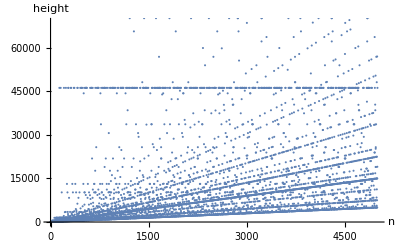

```mathematica
heightlist5=height5/@Range[5000];
ListPlot[heightlist5,AxesLabel->{"n","height"}]
```

```mathematica
Take[ReverseSortBy[Tally[heightlist5],Last],30]
```

{{46160,354},{1448,77},{10196,73},{13112,70},{3464,47},{5408,41},{8324,36},{1556,36},{7928,35},{11168,31},{548,31},{33632,30},{118088,29},{21860,28},{17648,26},{9296,26},{25748,24},{6416,23},{2816,23},{18944,21},{15488,20},{11816,20},{286352,19},{106424,19},{44288,19},{14084,19},{13760,19},{4472,19},{3392,19},{2096,19}}

Now, we’ll compute stopping times, or in other words the number of values in the sequence for a given n before we reach a cycle.

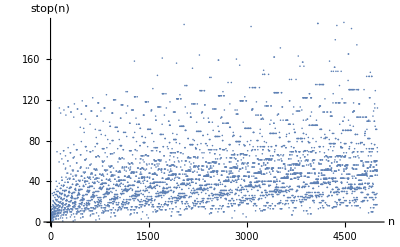

```mathematica
stop5[n_]:=Length[computeTrajectory5[n]]
stoplist5=stop5/@Range[5000];
ListPlot[stoplist5,AxesLabel->{"n","stop(n)"}]
```

For comparison, below are the corresponding height and stop time graphs for col(n):

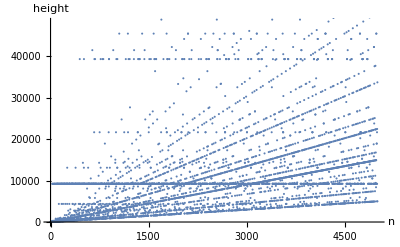

{{9232,1210},{39364,104},{4372,71},{250504,56},{21688,48},{13120,46},{2752,39},{8080,33},{95956,32},{14308,30},{190996,28},{45520,26},{5812,24},{1276936,23},{10528,22},{4192,22},{8584,21},{14560,19},{9448,18},{3616,18},{65608,17},{17332,17},{12148,17},{4264,17},{2248,17},{41524,16},{2896,16},{808,16},{1672,15},{24784,14}}

```mathematica
col[n_?OddQ]:=3n+1
col[n_?EvenQ]:=n/2
computeTrajectory[start_,maxIter_:100000]:=Module[{traj={start},n=start},
While[!MemberQ[{1,5,19,23,347,187},n]&&Length[traj]<maxIter,
n=col[n];
AppendTo[traj,n];
];
traj
]
height[n_]:=Max[computeTrajectory[n]]
heightlist=height/@Range[5000];
ListPlot[heightlist,AxesLabel->{"n","height"}]
Take[ReverseSortBy[Tally[heightlist],Last],30]
```

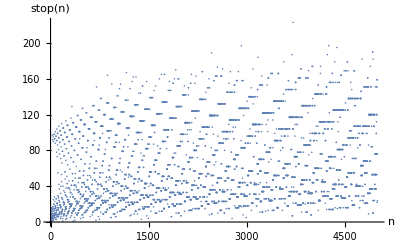

```mathematica
stop[n_]:=Length[computeTrajectory[n]]
stoplist=stop/@Range[5000];
ListPlot[stoplist,AxesLabel->{"n","stop(n)"}]
```

QUESTION 3 : What can we say about the heights and stop times of col5?
   
   The most common maximum height is 46160 with 354 occurrences for n from 1 to 5000. Other than that, there is no clear standout max height, with the next most common having only 77 occurrences . In the graph, much like for col[n], there are some pretty visible diagonal lines running out from the origin . 
  
  For stop times, there is not a very clear pattern . Much like col (n), there is not a strong relationship between n and the stop time of col5 (n) .
  
  
  QUESTION 4: Compare observations about col(n) and col5(n)
  
  For height, both col and col5 have one clear horizontal line, or in other words a clear most common max height. Col seems to have some fainter yet still clear horizontal lines. Additionally, col’s most common height occurs more than 20% of the time, a much much larger proportion than in col5.
  
  For stop time, the graphs look very very similar. Col seems to have more consistent groupings, with col5 having the same general pattern of little line segments, but less consistently grouped.